# Mutual Information

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dir ="../AnalysisData/best_categ_pass_agent/";
(*dir = "../AnalysisData/best_offset/";*)
```

## By Subtasks

### Over time

```mathematica
aaO=Import[StringJoin[dir,"mi_size_inT_A_avoid.dat"]];
acO=Import[StringJoin[dir,"mi_size_inT_A_pass.dat"]];
baO=Import[StringJoin[dir,"mi_size_inT_B_avoid.dat"]];
bcO=Import[StringJoin[dir,"mi_size_inT_B_catch.dat"]];
```

```mathematica
max=3.5;
```

"The instantaneous co-fluctuation magnitude between pairs of brain regions.. 
The instantaneous task-relevant information co-fluctuation magnitude between pairs of brain regions..

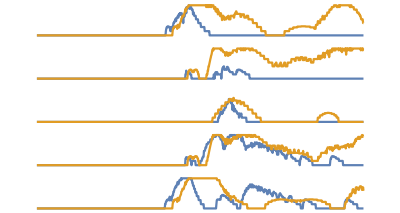

```mathematica
GraphicsColumn[
{
ListLinePlot[{baO[[1]],bcO[[1]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{baO[[2]],bcO[[2]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{baO[[3]],bcO[[3]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{baO[[4]],bcO[[4]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{baO[[5]],bcO[[5]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
```

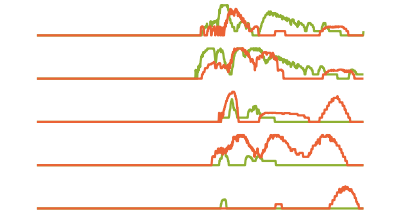

```mathematica
GraphicsColumn[
{
ListLinePlot[{aaO[[1]],acO[[1]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{aaO[[2]],acO[[2]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{aaO[[3]],acO[[3]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{aaO[[4]],acO[[4]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{aaO[[5]],acO[[5]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
```

### Time-averaged

```mathematica
aaT=Flatten[Import[StringJoin[dir,"mi_size_tavg_A_avoid.dat"]]];
acT=Flatten[Import[StringJoin[dir,"mi_size_tavg_A_pass.dat"]]];
baT=Flatten[Import[StringJoin[dir,"mi_size_tavg_B_avoid.dat"]]];
bcT=Flatten[Import[StringJoin[dir,"mi_size_tavg_B_catch.dat"]]];
```

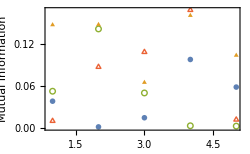

```mathematica
ListPlot[{baT,bcT,aaT,acT},PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotMarkers->{●,▲,○,△}]
```

## By Tasks

### Over time

```mathematica
aO=Import[StringJoin[dir,"mi_size_inT_A_both.dat"]];
bO=Import[StringJoin[dir,"mi_size_inT_B_both.dat"]];
```

### Time-averaged

```mathematica
aT=Flatten[Import[StringJoin[dir,"mi_size_tavg_A_both.dat"]]];
bT=Flatten[Import[StringJoin[dir,"mi_size_tavg_B_both.dat"]]];
```

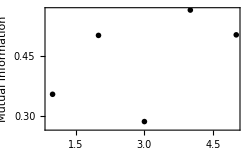

```mathematica
ListPlot[mi1,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●}]
```

## All data

### Over time

```mathematica
cO=Import[StringJoin[dir,"mi_size_inT_both_both.dat"]];
```

### Time-averaged

```mathematica
cT=Flatten[Import[StringJoin[dir,"mi_size_tavg_both_both.dat"]]];
```

```mathematica
ListPlot[mi1,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●}]
```

-Graphics-